```mathematica
pintegrand = 2*r*(1-(r-b)^2-4*b*r*Sin[x]^2)^(n/2)*(r-b+2*b*Sin[x]^2)
```

2 r (-b+r+2 b Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)

```mathematica
dpdr = D[pintegrand,r]
```

n r (-2 (-b+r)-4 b Sin[x]^2) (-b+r+2 b Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(-1+n/2)+2 r (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)+2 (-b+r+2 b Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)

```mathematica
dpdb = D[pintegrand,b]
```

n r (-b+r+2 b Sin[x]^2) (2 (-b+r)-4 r Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(-1+n/2)+2 r (-1+2 Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)

```mathematica
mn=(1-(r-b)^2-4*b*r*Sin[x]^2)^(n/2)
mnm2=(1-(r-b)^2-4*b*r*Sin[x]^2)^((n-2)/2)
dpdr2=2*r*((n+2)*mn-n*mnm2)
dpdb2=n/b*((r^2+b^2)*(mn-mnm2)+(r^2-b^2)^2*mnm2)
```

(1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)

(1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))

2 r (-n (1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(2+n) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2))

1/b n ((-b^2+r^2)^2 (1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(b^2+r^2) (-(1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)))

```mathematica
dpdrdiff = dpdr-dpdr2
```

n r (-2 (-b+r)-4 b Sin[x]^2) (-b+r+2 b Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(-1+n/2)+2 r (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)+2 (-b+r+2 b Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)-2 r (-n (1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(2+n) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2))

```mathematica
Simplify[%]
```

b (1-b^2-r^2+2 b r Cos[2 x])^(1/2 (-2+n)) (2 (-1+b^2+r^2) Cos[2 x]+b r (-2+n-(2+n) Cos[4 x]))

```mathematica
dpdbdiff = dpdb-dpdb2
```

n r (-b+r+2 b Sin[x]^2) (2 (-b+r)-4 r Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(-1+n/2)+2 r (-1+2 Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)-1/b n ((-b^2+r^2)^2 (1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(b^2+r^2) (-(1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)))

```mathematica
Simplify[%]
```

r (1-b^2-r^2+2 b r Cos[2 x])^(1/2 (-2+n)) (2 (-1+b^2+r^2) Cos[2 x]+b r (-2+n-(2+n) Cos[4 x]))

```mathematica
Integrate[dpdbdiff /. b -> 0.2 /. r -> 0.3 /. n -> 5,{x,-Pi/2,Pi/2}]
```

-2.54753×10^-16

```mathematica
pmn = 2*r^2*mn - n/(n+2)*((1-r^2-b^2)*mn+(1-(b-r)^2)*((b+r)^2-1)*mnm2)
```

2 r^2 (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)-1/(2+n)n ((1-(b-r)^2) (-1+(b+r)^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(1-b^2-r^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2))

```mathematica
FullSimplify[%]
```

-1/(2+n)2 r (1-b^2-r^2+2 b r Cos[2 x])^(1/2 (-2+n)) (r (b^2 (2+3 n)+(2+n) (-1+r^2))-b ((-1+b^2) n+(4+3 n) r^2) Cos[2 x])

```mathematica
NIntegrate[pintegrand /. b -> 0.2 /. r -> 0.2 /. n -> 5,{x,-Pi/2,Pi/2}]
```

0.18329

```mathematica
NIntegrate[pmn /. b -> 0.2 /. r -> 0.2 /. n -> 5,{x,-Pi/2,Pi/2}]
```

0.18329

```mathematica
pintegrand - pmn
```

-2 r^2 (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)+2 r (-b+r+2 b Sin[x]^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2)+1/(2+n)n ((1-(b-r)^2) (-1+(b+r)^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(1/2 (-2+n))+(1-b^2-r^2) (1-(-b+r)^2-4 b r Sin[x]^2)^(n/2))

```mathematica
FullSimplify[%]
```

(2 b r (1-b^2-r^2+2 b r Cos[2 x])^(1/2 (-2+n)) (2 (-1+b^2+r^2) Cos[2 x]+b r (-2+n-(2+n) Cos[4 x])))/(2+n)

```mathematica
NIntegrate[pintegrand - pmn/. b -> 0.2 /. r -> 0.2 /. n -> 5,{x,-Pi/2,Pi/2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.5707962986223783009641881426199410331720485167750211985548958182}. NIntegrate obtained -1.08691×10^-16 and 8.98686×10^-15 for the integral and error estimates.

-1.08691×10^-16

```mathematica
NIntegrate[pintegrand - pmn/. b -> 0.99 /. r -> 0.1 /. n -> 5  ,{x,-ArcSin[Sqrt[(1-(r-b)^2)/(4*b*r)]]/.b -> 0.99 /. r -> 0.1 ,ArcSin[Sqrt[(1-(r-b)^2)/(4*b*r)]]/. b -> 0.99 /. r -> 0.1 }]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0601349}. NIntegrate obtained 2.16967×10^-18 and 6.47699×10^-20 for the integral and error estimates.

2.16967×10^-18

```mathematica
NIntegrate[dpdrdiff /. b -> 0.2 /. r -> 0.2 /. n -> 5, {x,-Pi/2,Pi/2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.81725×10^-8}. NIntegrate obtained 3.81639×10^-17 and 2.48206×10^-13 for the integral and error estimates.

3.81639×10^-17

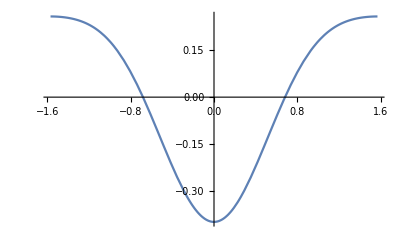

```mathematica
Plot[dpdrdiff /. b -> 0.2 /. r -> 0.2 /. n -> 5, {x,-Pi/2,Pi/2}]
```